```mathematica
(*Question 1a*)
j=I;
RadToDeg[x_]:=x*180/Pi
UnitstepRange[x_,a_,b_]:=UnitStep[x-a]-UnitStep[x-b]
SignalEnergy[x_]:=Limit[Integrate[Abs[x]^2,{t,-T,T}],T->Infinity]
SignalPower[x_]:=Limit[1/(2T)SignalEnergy[x],T-> Infinity]
```

```mathematica
(*Question 3*)
Integrate[Sin[Pi t]DiracDelta[t-2],{t,-Infinity, 1}]
```

0

```mathematica
(*Question 4*)
Integrate[t,{t,0,1}]
```

1/2

2/5

(2 Sin[(n π)/5])/(n π)

0

0

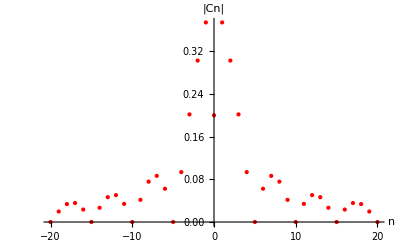

```mathematica
(*Question 5*)
T0=10 Pi;
W0=1/5;
A0=2/T0 Integrate[1,{t,-Pi,Pi}]
An=2/T0 Integrate[Cos[n W0 t],{t,-Pi,Pi}]
Bn=2/T0 Integrate[Sin[n W0 t],{t,-Pi,Pi}]
Cn=Piecewise[{
{√(An^2+Bn^2),n≠0 },
{A0/2,n==0}
}];
θn=ArcTan[-Bn/An];
An/.{n-> 10}
Cn Cos[n W0 t+θn ];
ListPlot[Table[{n,Cn},{n,-20,20}],
PlotStyle->{Red,PointSize[Medium]},
AxesLabel->{"n","|Cn|"},
PlotRange->All]
```

-Cos[π/6-5 t]-3 Sin[π/6-7 t]+Sin[3 t]

-1/2 √3 Cos[5 t]-3/2 Cos[7 t]+Sin[3 t]-1/2 Sin[5 t]+3/2 √3 Sin[7 t]

-Cos[30 °-5 t]-3 Sin[30 °-7 t]+Sin[3 t]

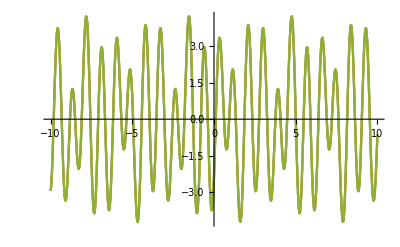

```mathematica
(*Question 6*)
g=Sin[3t]+Sin[5 t-(2Pi)/3]-3 Cos[7 t+Pi/3]
g2=g//TrigToExp//FullSimplify//Expand
ω0=GCD[3,5,7];
a3=0;
b3=1;
D3=√(a3^2+b3^2);
a5=(-√3)/2;
b5=-1/2;
D5=√(a5^2+b5^2);
a7=-3/2;
b7=(3 √3)/2;
D7=√(a7^2+b7^2);
g3=Cos[3t+270Degree]+Cos[5t+150Degree]+3Cos[7t+240Degree]
Plot[{g,g2,g3},{t,-10,10}]
```

ⅇ^(ⅈ n π) (ⅈ/(n^3 π^3)+1/(n^2 π^2)-ⅈ/(2 n π))+ⅇ^(-ⅈ n π) (-ⅈ/(n^3 π^3)+1/(n^2 π^2)+ⅈ/(2 n π))

a_0: 2/3

a_n: (4 Cos[n π])/(n^2 π^2)-(4 Sin[n π])/(n^3 π^3)+(2 Sin[n π])/(n π)

b_n: 0

C_n: (4 Cos[n π])/(n^2 π^2)-(4 Sin[n π])/(n^3 π^3)+(2 Sin[n π])/(n π)

θ_n: 0

D_n: ⅇ^(ⅈ n π) (ⅈ/(n^3 π^3)+1/(n^2 π^2)-ⅈ/(2 n π))+ⅇ^(-ⅈ n π) (-ⅈ/(n^3 π^3)+1/(n^2 π^2)+ⅈ/(2 n π))

D_-n: ⅇ^(ⅈ n π) (ⅈ/(n^3 π^3)+1/(n^2 π^2)-ⅈ/(2 n π))+ⅇ^(-ⅈ n π) (-ⅈ/(n^3 π^3)+1/(n^2 π^2)+ⅈ/(2 n π))

|D_n|: 1/2 ((4 Cos[n π])/(n^2 π^2)-(4 Sin[n π])/(n^3 π^3)+(2 Sin[n π])/(n π))

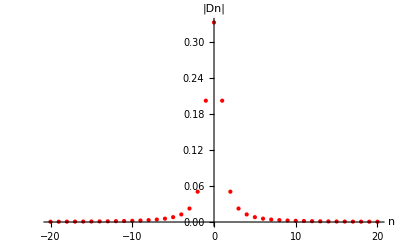

```mathematica
(*Question 7*)
j=I;
Plot[
(Mod[t+1,2]-1)^2,{t,-3,3},
PlotRange->All,
AxesLabel->{"t","x(t)"},
GridLines->Automatic
];
T0=2;
W0=(2 Pi)/T0;
A0=2/T0 Integrate[t^2,{t,-1,1}];
An=2/T0 Integrate[t^2 Cos[n W0 t],{t,-1,1}]//Expand;
Bn=2/T0 Integrate[t^2 Sin[n W0 t],{t,-1,1}];
Cn=An-j Bn;
θn=ArcTan[-Bn/An];
Dn=Cn/2//TrigToExp;
Dn=Collect[Dn,E^(j n Pi)]
DnMag=(√(An^2+Bn^2))/2//PowerExpand;
Print["a_0: ",A0]
Print["a_n: ",An]
Print["b_n: ",Bn]
Print["C_n: ",Cn]
Print["θ_n: ",θn]
Print["D_n: ",Dn]
Print["D_-n: ",Dn/.{n-> -n}]
Print["|D_n|: ",DnMag]

DnMag=Piecewise[{
{(√(An^2+Bn^2))/2,n≠0 },
{A0/2,n==0}
}];
ListPlot[Table[{n,DnMag},{n,-20,20}],
PlotStyle->{Red,PointSize[Medium]},
AxesLabel->{"n","|Dn|"},
PlotRange->All]
```

```mathematica
Nmax=100;
f[t_]:=A0/2+Sum[Dn E^(j n W0 t)+Dn E^(-j n W0 t),{n,1,Nmax}]

(*Display the result*)
Plot[f[t],{t,-10,10}]
```

-Graphics-

ⅇ^(-2/3 ⅈ n π) (3/(4 n^2 π^2)+ⅈ/(2 n π))-3/(4 n^2 π^2)

a_0: 1/3

a_n: -3/(2 n^2 π^2)+(3 Cos[(2 n π)/3])/(2 n^2 π^2)+Sin[(2 n π)/3]/(n π)

b_n: (-6 n π Cos[(2 n π)/3]+9 Sin[(2 n π)/3])/(6 n^2 π^2)

C_n: -3/(2 n^2 π^2)+(3 Cos[(2 n π)/3])/(2 n^2 π^2)+Sin[(2 n π)/3]/(n π)-(ⅈ (-6 n π Cos[(2 n π)/3]+9 Sin[(2 n π)/3]))/(6 n^2 π^2)

θ_n: -ArcTan[(-6 n π Cos[(2 n π)/3]+9 Sin[(2 n π)/3])/(6 n^2 π^2 (-3/(2 n^2 π^2)+(3 Cos[(2 n π)/3])/(2 n^2 π^2)+Sin[(2 n π)/3]/(n π)))]

D_n: ⅇ^(-2/3 ⅈ n π) (3/(4 n^2 π^2)+ⅈ/(2 n π))-3/(4 n^2 π^2)

D_-n: ⅇ^((2 ⅈ n π)/3) (3/(4 n^2 π^2)-ⅈ/(2 n π))-3/(4 n^2 π^2)

|D_n|: 1/2 √((-6 n π Cos[(2 n π)/3]+9 Sin[(2 n π)/3])^2/(36 n^4 π^4)+(-3/(2 n^2 π^2)+(3 Cos[(2 n π)/3])/(2 n^2 π^2)+Sin[(2 n π)/3]/(n π))^2)

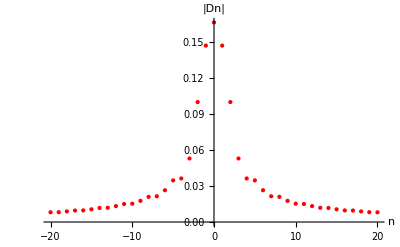

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/π encountered.

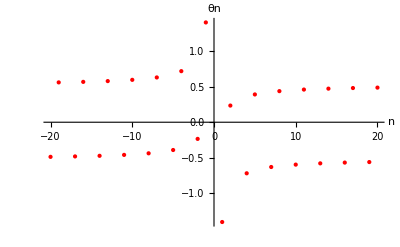

```mathematica
(*Question 8*)
j=I;
T0=3;
W0=(2 Pi)/T0;
A0=2/T0 Integrate[t,{t,0,1}];
An=2/T0 Integrate[t Cos[n W0 t],{t,0,1}]//Expand;
Bn=2/T0 Integrate[t Sin[n W0 t],{t,0,1}];
Cn=An-j Bn;
θn=ArcTan[-Bn/An];
Dn=Cn/2//TrigToExp;
Dn=Collect[Dn,E^(j n Pi)]
DnMag=(√(An^2+Bn^2))/2//PowerExpand;
Print["a_0: ",A0]
Print["a_n: ",An]
Print["b_n: ",Bn]
Print["C_n: ",Cn]
Print["θ_n: ",θn]
Print["D_n: ",Dn]
Print["D_-n: ",Dn/.{n-> -n}]
Print["|D_n|: ",DnMag]

DnMag=Piecewise[{
{(√(An^2+Bn^2))/2,n≠0 },
{A0/2,n==0}
}];
ListPlot[Table[{n,DnMag},{n,-20,20}],
PlotStyle->{Red,PointSize[Medium]},
AxesLabel->{"n","|Dn|"},
PlotRange->All]

ListPlot[Table[{n,θn},{n,-20,20}],
PlotStyle->{Red,PointSize[Medium]},
AxesLabel->{"n","θn"},
PlotRange->All]
```

ⅇ^((2 ⅈ n π)/3) (3/(4 n^2 π^2)-ⅈ/(2 n π))-3/(4 n^2 π^2)

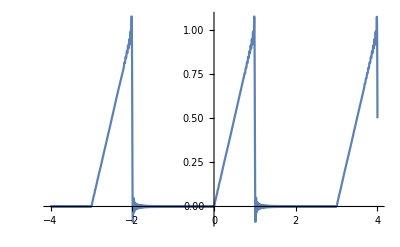

```mathematica
Nmax=100;
nDn=Dn/.{n-> -n}
f[t_]:=A0/2+Sum[Dn E^(j n W0 t)+nDn E^(-j n W0 t),{n,1,Nmax}]

(*Display the result*)
Plot[f[t],{t,-4,4}]
```